```mathematica
(* This notebook creates the M function out of a spectral density *)
const5305=
1.0/2.0/Pi/2.99792458*100000
```

5308.84

```mathematica
Temperature =  77;
kBT = 0.69503476636299999*Temperature
```

53.5177

```mathematica
Λ=const5305/100.0
```

53.0884

```mathematica
Clear[Spd1,Spd2]
```

```mathematica
Spd1[x_]=2*1 *x*Λ/(x^2 + Λ^2)
```

(106.177 x)/(2818.38+x^2)

```mathematica
Spd2[x_]=1* x/ Λ ⅇ^(-x/Λ)
```

0.0188365 ⅇ^(-0.0188365 x) x

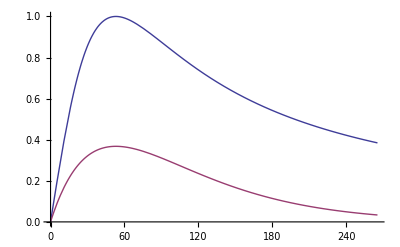

```mathematica
Plot[{Spd1[x],Spd2[x]},{x,0,5*Λ}]
```

```mathematica
Num=1000;
dω=2
NumT=2*Num; 
β=1/kBT; 
Ω=dω*NumT; dt=2.0π/Ω
```

2

0.0015708

```mathematica
nSpd1=Array[Spd1[dω*#]&,Num,0];
nSpd2=Array[Spd2[dω*#]&,Num,0];
```

```mathematica
tim=Array[dt* # &,NumT,0];
timpos=Array[dt* # &,Num,0];
(* positive time part - and negative *)
For[i=Num,i<NumT,i++,
tim[[i+1]]= - tim[[NumT-i+1]];
];
 (* ListPlot[tim,PlotRange->All] *)
```

```mathematica
(* making the frequency range *)
freq = Array[dω* # &,NumT,0];
freqpos = Array[dω* # &,Num,0];
(* that was only positive part - negative *)
For[i=Num,i<NumT,i++,
freq[[i+1]]= - freq[[NumT-i+1]];
];
 (* ListPlot[freq,PlotRange->All] *)
```

0.0752393

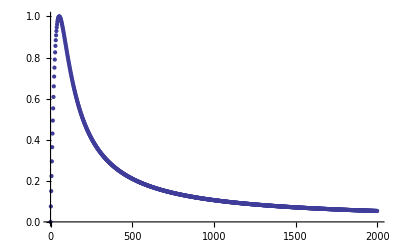

```mathematica
(* Choosing the spectral density *)
nSpd = nSpd1;
nSpd[[2]]
(* the spectral density contains only positive partt *)
ListPlot[Transpose[{freqpos,nSpd}],PlotRange->{{0,Num*dω},All}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

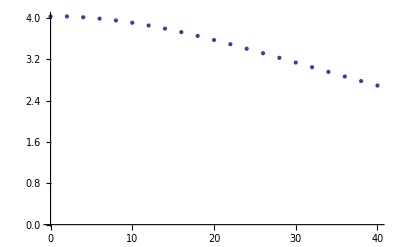

53.5177

```mathematica
(* checking if steps are OK for coth *)
aTest = nSpd*Coth[freqpos*β/2];
aTest[[1]] = nSpd[[2]]  *2.0/β  /dω; 
ListPlot[Transpose[{freqpos,aTest}],PlotRange->{{0,20*dω},All}]
1.0/β
```

```mathematica
Cort = Array[#&,Num]; (* creating the correlation function only for positive time *)
```

```mathematica
(* only positive time will be calculated *)
For[i=0,i<Num,i++,
cval = 0.0;
t = dt i;

cval += nSpd[[2]]  *2.0/β  /dω; (* zero frequency element taken from derivative value *)

For[j=1,j<Num,j++, (* positive *)
ω = dω j;
(* positive frequency part *)
cval += nSpd[[j+1]]*(Cos[t*ω]Coth[ω*β/2.0]-I*Sin[t*ω]);
];

For[j=1,j<Num,j++, (* negative *)
(* the last point is absent so we set it to 0 *)
ω = -dω j; 
cval += -nSpd[[j+1]]*(Cos[t*ω]Coth[ω*β/2.0]-I*Sin[t*ω]);
];
(* assignment *)
Cort[[i+1]]=cval*dω/(2π);
];
(* that was only positive time part - negative will be conjugate *)
```

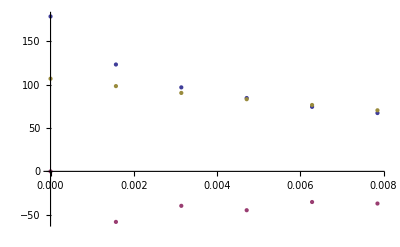

178.908+0. ⅈ

97.0145-39.7773 ⅈ

```mathematica
CortR = Re[Cort];CortI = Im[Cort];
ListPlot[
{Transpose[{timpos,CortR}],
Transpose[{timpos,CortI}],
Transpose[{timpos,2*kBT*Exp[-Λ*timpos]}]},
PlotRange->{{0,Num*dt/200},All}]
Cort[[1]]
Cort[[3]]
```

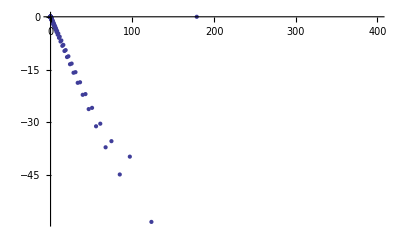

```mathematica
CortR = Re[Cort];CortI = Im[Cort];ListPlot[{Transpose[{CortR,CortI}]},PlotRange->{{0,400},All}]
```

```mathematica
MfunP = Array[#&,NumT]; (* using the meaning of the Fourier transform *)
```

```mathematica
(* A positive half integral of the Correlation function *)

(* positive and negative frequencies *)
For[i=0,i<NumT,i++,
om = 0.0;
If[i< Num,
om = dω * i;,
om = dω * (i-NumT);];

cval = Cort[[1]]/2.0; (* zero time /2 due to one-side integral *)

For[j=1,j<Num,j++, (* time integral *)
ti = dt j;
cval += Cort[[j+1]]*Exp[I*om*ti];
];
MfunP[[i+1]]=cval*dt;
];
```

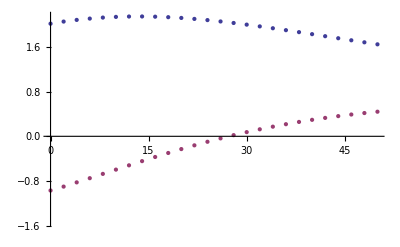

```mathematica
MfunPR=Re[MfunP]; MfunPI=Im[MfunP];
ListPlot[
{Transpose[{freq,MfunPR}],
Transpose[{freq,MfunPI}]},
PlotRange->{{0,Num*dω/40},All}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

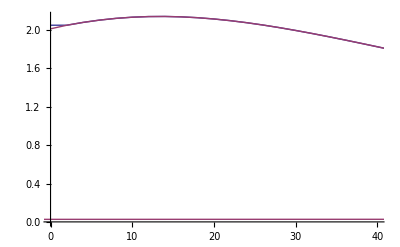

```mathematica
(* Last comparison of a real part: *)
aTest = nSpd*(Coth[freqpos*β/2]+1)/2;
aTest[[1]] = nSpd[[2]]  *2.0/β  /dω /2 + nSpd[[2]] /2 ; 
ListLinePlot[
{Transpose[{freqpos,aTest}],
Transpose[{freq,MfunPR}]},
PlotRange->{{0,20*dω},All}]
```

```mathematica
(* SetDirectory["C:\\Users\\Darius\\My Documents"] *)
```

```mathematica
(* Export["outCorf.tsv",Transpose[{tim,CortR,CortI}]] *)
```

```mathematica
(* Export["outMfun.tsv",Transpose[{freq,MfunPR,MfunPI}]] *)
```

```mathematica
(* dataset = {Num,dω, β, Ω, dt,freq,nSpd,Cort,MfunP};
DumpSave["datasetcorrFunct.mx",dataset]  *)
```

```mathematica
MfunP[[1]] 
MfunP[[2]] 
MfunP[[3]] 
dω
```

2.01333-0.968885 ⅈ

2.05115-0.899098 ⅈ

2.08066-0.823452 ⅈ

2

```mathematica
2
```

2

```mathematica
(* Making g-funtion *)
gfun = Array[#&,Num]; (* creating the lineshape function only for positive time *)
(* direct calculation from the correlation function *)
dt2 = dt*dt;
gfun[[1]] = 0;
cval = 0.0;

For[i=1,i<Num,i++,(* this is time variable *)

(* B integral *)
cval =  Cort[[1]]/2.0;
For[j=2 ,j<i,j++, (* first integral positive *)
cval +=  Cort[[j]];
];

(* Cn *)
cval +=  Cort[[i]]*7.0/8.0 ;

(* Cn+1 *)
cval +=  Cort[[i+1]]*1.0/8.0 ;

cval *= dt2;

cval += gfun[[i]];
gfun[[i+1]] = cval; 
];
(* that was only positive time part - negative will be conjugate *)
```

```mathematica
gfun[[1+1]]
gfun[[2+1]]
gfun[[10+1]]
dt
Cort[[1]]

Cort[[2]]

Cort[[3]]
```

0.000645044-0.000017993 ⅈ

0.00116215-0.000156212 ⅈ

0.0120385-0.00456699 ⅈ

0.0015708

178.908+0. ⅈ

123.424-58.3382 ⅈ

97.0145-39.7773 ⅈ

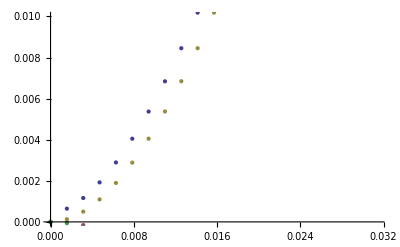

```mathematica
gfR = Re[gfun];gfI = Im[gfun];
ListPlot[
{Transpose[{timpos,gfR}],
Transpose[{timpos,gfI}],
Transpose[{timpos,(2*kBT*1/Λ^2)*(Exp[-Λ*timpos]+Λ*timpos-1.0)}]
 ,Transpose[{timpos,-1/Λ*(Exp[-Λ*timpos]+Λ*timpos-1.0)}] },
PlotRange->{{0,Num*dt/50},{0,0.01}}]
```